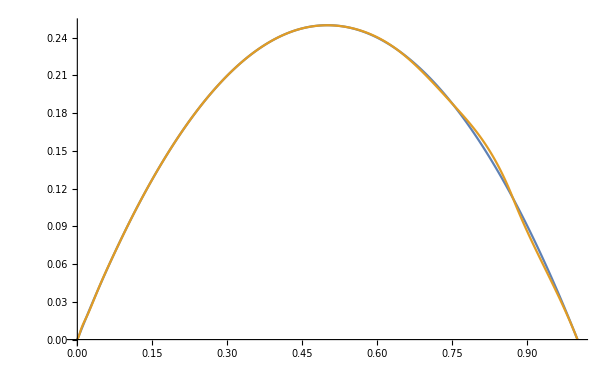

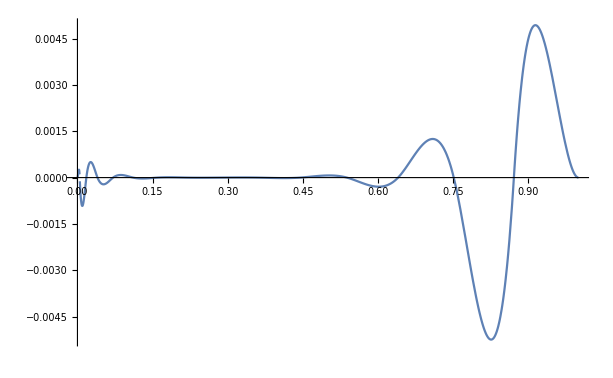

```mathematica
(* Функция за интерполиране *)
f[t_]:= t(1-t);

(* Интервал *) 
intervalStart = 0;
intervalEnd = 1;

(* Брой интерполационни възли *)
n=15;

(* Интерполационни възли *)
Do[x[k]=(k/n)^2,{k,0,n}];

(* Търсим делта, което е разстоянието между съседните възли *)
Do[delta[k]=x[k+1]-x[k],{k,0,n-1}]; 

(* Решаване на системата по метода на прогонката *) 
Do[A[k]=1/delta[k-1],{k,2,n - 1}];
Do[B[k]=2/delta[k-1]+2/delta[k],{k,1, n - 1}];
Do[coefC[k]=1/delta[k],{k, 1,n-2}];
Do[value[k]=3*(f[x[k]]-f[x[k-1]])/delta[k-1]^2+3*(f[x[k+1]]-f[x[k]])/delta[k]^2,{k,1,n-1}];

(* Намираме коефициентите алфа и бета *)
alpha[1]=-coefC[1]/B[1];
beta[1]=value[1]/B[1];
Do[alpha[k]=-coefC[k]/(A[k]*alpha[k-1]+B[k]),{k,2,n-2}];
Do[beta[k]=(value[k]-A[k]*beta[k-1])/(A[k]*alpha[k-1]+B[k]),{k,2,n-1}];

(* Намираме d[0] i d[n] с помощта на първа производна на f(x) *)
d[0] =f'[x[0]];
d[n] = f'[x[n]];

(* Намираме d[n-1] чрез бета *)
d[n-1]=beta[n-1];


Do[d[k]=alpha[k]*d[k+1]+beta[k],{k,n-2,1,-1}];
Do[a[k]=d[k+1]/delta[k]^2+d[k]/delta[k]^2+2*(f[x[k]]-f[x[k+1]])/delta[k]^3,{k,0,n-1}];
Do[b[k]=(f[x[k+1]]-f[x[k]])/delta[k]^2-d[k]/delta[k],{k,0,n-1}];

(* Намираме общия вид на полиномите, които интерполират f(х) във всеки подинтервал на [0, 1],определен от два последователни интерполационни възела *)
Do[withPolinom[k,z_]=a[k]*(z-x[k])^2*(z-x[k+1])+b[k]*(z-x[k])^2+d[k]*(z-x[k])+f[x[k]],{k,0,n-1}];

(* Построяваме на кубичния сплайн за f(х),имайки интерполиращите полиноми за всеки един интервал, използвайки рекурсия*)
rec[i_,t_]:=If[i≤n+1,If[t≥x[i]&&t<x[i+1],withPolinom[i,t],rec[i+1,t]]];

spline[t_]:=rec[0,t];

(* Графика на функцията и сплайн функцията *)
Plot[{f[t],spline[t]}, {t, intervalStart, intervalEnd}, PlotPoints->400]

(* Графика на разликата от функцията и сплайн функцията *)
Plot[f[t]-spline[t] , {t, intervalStart, intervalEnd}, PlotRange->All]
```